# Aerosol microphysics model

## Constants

```mathematica
molecWgtDryAir = Quantity[28.966,"g/mole"];
rdry = UnitConvert[Quantity["MolarGasConstant"]/molecWgtDryAir];
g=UnitConvert[Quantity["StandardAccelerationOfGravity"]];
gammaDry = UnitConvert[Quantity[0.098,"Kelvin/km"]];
```

0.000098 K/m

## Particle size distributions

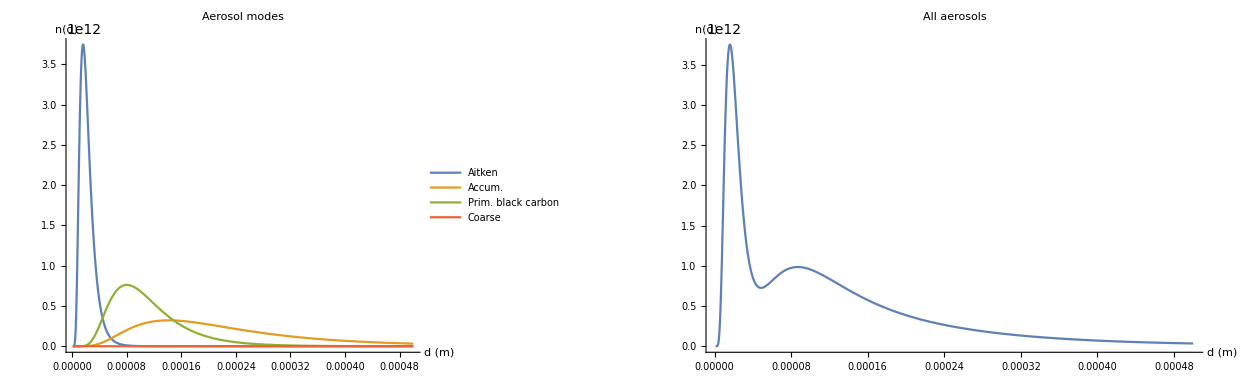

/Users/pabosle/haero/docs/design/figures/modes_pdf_example.png

/Users/pabosle/haero/docs/design/figures/sum_pdf_example.png

/Users/pabosle/haero/docs/design/figures/pdf_examples.png

```mathematica
ndist[diam_,num_,geoMean_,dev_]:=num*Exp[-(Log[diam]-Log[geoMean])^2/(2Log[dev]^2)]/(Sqrt[2Pi] diam Log[dev]);
aitken[diam_]:=ndist[diam,79030830.111949,20 *10^(-6),1.6];
accum[diam_]:=ndist[diam, 79696874.4450315,200*10^(-6),1.8];
pbcarbon[diam_]:=ndist[diam,80360691.2808247,100*10^(-6),1.6];
coarse[diam_]:=ndist[diam,81022287.9166187,2000*10^(-6),1.6];
pltfntsize = 18;
modesplot=Plot[{aitken[d],accum[d],pbcarbon[d],coarse[d]},{d,1*10^(-6),0.0005},PlotRange->All,PlotLegends->Placed[{"Aitken","Accum.","Prim. black carbon", "Coarse"},{Right,Center}],PlotLabel->"Aerosol modes",AxesLabel->{"d (m)", "n(d)"},ImageSize->Large,BaseStyle->{FontSize->pltfntsize}];
sumplot =Plot[aitken[d]+accum[d]+pbcarbon[d]+coarse[d],{d,1*10^(-6),0.0005},PlotRange->All,PlotLabel->"All aerosols",AxesLabel->{"d (m)", "n(d)"},ImageSize->Large,BaseStyle->{FontSize->pltfntsize}];
rowplot = GraphicsRow[{modesplot,sumplot}]
Export[ToString[Directory[]]<>"/haero/docs/design/figures/pdf_examples.png",rowplot]
```

```mathematica
moment[k_]:=Assuming[σ>1,Integrate[d^k ndist[d,n,gm,σ],{d,0,Infinity}]];
mbar[k_]:=moment[k]/n;
Table[moment[k],{k,0,3}]
Table[mbar[k],{k,0,3}]
```

{n,ⅇ^(Log[σ]^2/2) gm n,ⅇ^(2 Log[σ]^2) gm^2 n,ⅇ^((9 Log[σ]^2)/2) gm^3 n}

{1,ⅇ^(Log[σ]^2/2) gm,ⅇ^(2 Log[σ]^2) gm^2,ⅇ^((9 Log[σ]^2)/2) gm^3}

## Test cases

### Prescribed velocity

Height in meters; time in seconds; default period = 8 hours.

```mathematica
prescw[z_,t_, wmax_:2, tperiod_:8*3600,ztop_:10000]:= wmax Cos[2Pi t/tperiod]Sin[2Pi z/ztop];
prescdwdz[z_,t_,wmax_:2,tperiod_:8*3600,ztop_:10000]:=D[w[z,t,wmax,tperiod,ztop],z];
```

### Temperature profiles

Constant lapse rate (static stability determined by lapse rate)
Temperature in Kelvin

```mathematica
staticStability[Γ_]:=If[Γ<QuantityMagnitude[gammaDry],"Stable",If[Γ==QuantityMagnitude[gammaDry],"Neutral",False]];
tempProfile[z_,T0_:290,Γ_:0]:=T0-Γ z;
```

### Hydrostatic balance

```mathematica
Clear[p,pz,heqn,pzsol,dryhydro, g, rdry]
hydro = {D[p[z],z]==-g  p[z]/(R (Subscript[T, 0] - Γ z)),p[0]==100000};
DSolve[hydro,p[z],z]
(*dryhydro[T0_:290,Γ_:0]:= {D[p[z],z]==-p[z]*QuantityMagnitude[g]/(QuantityMagnitude[rdry]*tempProfile[z,T0,Γ]),p[0]==100000};
heqn = dryhydro[290,0.5*QuantityMagnitude[gammaDry]];
pzsol = NDSolve[heqn,p[z],{z,0,10000}];
Plot[{p[z]/.pzsol},{z,0,10000},PlotRange->{{0,10000},{0,100000}}]*)
```

{{p[z]→100000 (-R T_0)^(-g/(R Γ)) (R z Γ-R T_0)^(g/(R Γ))}}